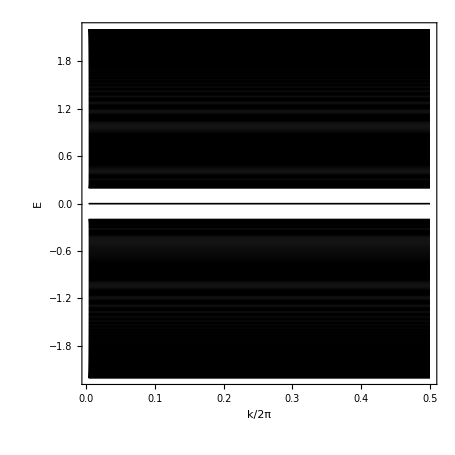

```mathematica
n=500;
ham[v_,w_]:=SparseArray[{{i_,j_}/;i==j+1:>If[EvenQ[i],v,w],{j_,i_}/;i==j+1:>If[EvenQ[i],v,w]},{n,n}]
es=Eigensystem[ham[1.,1.2]//Normal];
bandSpectrum=MapThread[{Table[{i*2./n,#1},{i,1,n/4}],Abs[Fourier[#2[[;;;;2]]][[;;n/4]]]}&,es];
bandSpectrum={#[[1]],#[[2]]/Max[bandSpectrum[[All,2]]]}&/@bandSpectrum;
Graphics[Line[#[[1]],VertexColors->(ColorData["TemperatureMap"]/@#[[2]])]&/@bandSpectrum,Frame->True,FrameLabel->{"k/2π","E"},AspectRatio->1]
```